## Cell Division Axis

### scratch work

```mathematica
Clear[α,β];
DeleteDuplicates@Flatten@Fold[Insert[#1,#2[[2]],#2[[1]]]&,{{a,b},{b,c},{c,d},{d,e},{e,a}},{{{4,2},β},{{3,2},α}}]
```

{a,b,c,α,d,β,e}

```mathematica
Flatten@SequenceCases[{a,b,c,α,d,β,e},{___,α}|{β,___}]
```

{a,b,c,α,β,e}

```mathematica
Flatten@SequenceCases[{a,b,c,α,d,β,e},{α,__,β}]
```

{α,d,β}

### finding axis of division

```mathematica
Clear[centroidPolygon];
centroidPolygon[vertices_]:=Mean@vertices
```

```mathematica
(* allow cells to divide *)
```

```mathematica
me=Polygon[…];
```

```mathematica
p=MeshPrimitives[me,0]/.Point->Sequence
```

{{0.190657,0.259949},{0.340267,0.0238182},{0.40141,0.146524},{0.985985,0.0397145},{0.226276,0.534713}}

```mathematica
Evaluate[Table[{Subscript[x, i],Subscript[y, i]},{i,6}]]=Append[p,First@p];
```

```mathematica
Subscript[I, xx]=1/12 ∑_(i=1)^5 (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[y, i]^2+Subscript[y, i] Subscript[y, i+1]+Subscript[y, i+1]^2)
```

0.0108197

```mathematica
Subscript[I, yy]=1/12 ∑_(i=1)^5 (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[x, i]^2+Subscript[x, i] Subscript[x, i+1]+Subscript[x, i+1]^2)
```

0.036854

```mathematica
Subscript[I, xy]=1/24 ∑_(i=1)^5 (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[x, i] Subscript[y, i+1]+2 Subscript[x, i] Subscript[y, i]+2 Subscript[x, i+1] Subscript[y, i+1]+Subscript[x, i+1] Subscript[y, i])
```

0.0152804

```mathematica
mat=({{Subscript[I, xx], -Subscript[I, xy]}, {-Subscript[I, xy], Subscript[I, yy]}})
```

{{0.0108197,-0.0152804},{-0.0152804,0.036854}}

```mathematica
Eigensystem[mat]
```

{{0.0439101,0.00376355},{{-0.419236,0.907877},{-0.907877,-0.419236}}}

```mathematica
eigvals=Eigenvalues[mat]
```

{0.0439101,0.00376355}

```mathematica
eigvectors=Eigenvectors[mat]
```

{{-0.419236,0.907877},{-0.907877,-0.419236}}

```mathematica
pos=Position[eigvals,Max[eigvals]];
```

```mathematica
cent=RegionCentroid[me];
```

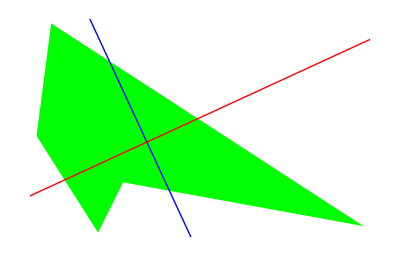

```mathematica
Graphics[{{Green,me},Thick,Blue,InfiniteLine[{cent,cent+Extract[eigvectors,pos][[1]]}],Red,InfiniteLine[{cent,cent+Extract[eigvectors,{{2}}][[1]]}]}]
```

```mathematica
edges=Partition[p,2,1,1];
```

```mathematica
edgePart=Line/@Partition[p,2,1,1];
```

```mathematica
intersects=RegionIntersection[InfiniteLine[{cent,cent+Extract[eigvectors,pos][[1]]}],#]&/@edgePart;
```

```mathematica
intersectPts=Cases[intersects,{__Real},{3}];
```

```mathematica
posIntersects=Flatten@Position[intersects,_Point,{1}];
```

```mathematica
repPart=Thread[{posIntersects,2}];
```

```mathematica
{α,β}=intersectPts;
```

```mathematica
inserts=Reverse@Thread[{repPart,intersectPts}];
```

```mathematica
withAdditions=DeleteDuplicates@Flatten[Fold[Insert[#1,#2[[2]],#2[[1]]]&,edges,inserts],1];
```

```mathematica
(* i=0;
Insert[p,"mark",{{4},{5}}]/."mark":>(++i;intersectPts[[i]])//Trace*)
```

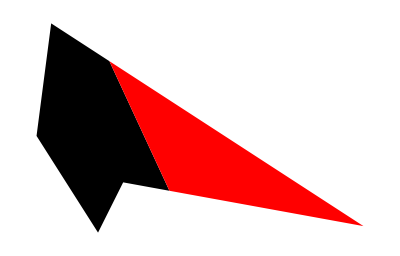

```mathematica
Graphics[{Black,Polygon[Join@@SequenceCases[withAdditions,{___,α}|{β,___}]],Red,Polygon[Join@@SequenceCases[withAdditions,{α,__,β}]]}]
```

```mathematica
Table[{Unevaluated[Subscript[x,j]]=.,Unevaluated[Subscript[y,j]]=.},{j,Length[p]+1}];
```

## Initialize mesh

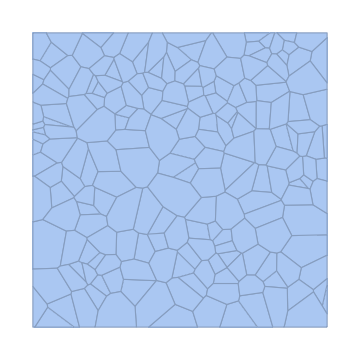

```mathematica
SeedRandom[3]
mesh=VoronoiMesh[RandomReal[1,{200,2}],{{0,1},{0,1}},ImageSize-> Medium]
```

```mathematica
pts=MeshPrimitives[mesh,0]/.Point->Sequence;
```

```mathematica
cornerpts=pts[[-4;;]];
pts=pts[[1;;-5]];
```

```mathematica
ptsToInd=AssociationThread[pts-> Range@Length[pts]];
indToptsC=indTopts=AssociationMap[Reverse][ptsToInd];
```

```mathematica
cellmeshprim=MeshPrimitives[mesh,2];
cells=(MeshPrimitives[#,0]&/@cellmeshprim)/.Point->Sequence/.Thread[cornerpts->Nothing];
```

```mathematica
cellToVertexG=AssociationThread[Range[Length@cells]->Map[ptsToInd,cells,{2}]];
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
```

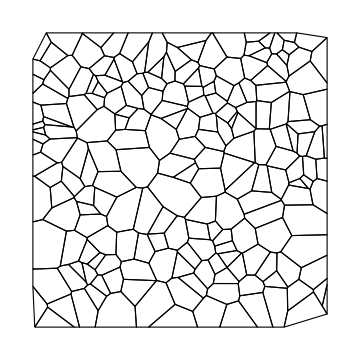

```mathematica
plt=Graphics[Map[{FaceForm[None],EdgeForm[Black],Polygon@Lookup[indTopts,#]}&,Values@cellToVertexG],ImageSize->Medium]
```

```mathematica
Clear[areaOfPolygon];
areaOfPolygon[cells_/;Head[cells]===Association]:=Map[Area@*Polygon,cells];
```

```mathematica
Clear[areaPolygon];
areaPolygon[vertices_]:=Block[{edges},
edges=Partition[vertices,2,1,1];
0.5Abs@Total[(#[[1,1]]*#[[2,2]])-(#[[2,1]]*#[[1,2]])&/@edges]
]
```

```mathematica
Clear[perimeterOfPolygon];
perimeterOfPolygon[cells_/;Head[cells]===Association]:=(Perimeter@*Polygon)/@cells;
```

```mathematica
Clear[perimeterPolygon];
perimeterPolygon[vertices_]:=Block[{edges},
edges=Partition[vertices,2,1,1];
Total[Apply[EuclideanDistance]/@edges]
]
```

```mathematica
Clear[cellDivision];
cellDivision[polygonind_,indToPoints_,areaAssoc_,perimAssoc_,cellToVertG_]:=Block[{x,y,num,matrix,xx,xy,yy,eigvals,eigVecs,maxeigpos,cent,edges,edgesL,intersects,intersectionPts,posIntersections,repPart,α,β,polygonPts,newkeys=Range[#+1,#+2]&[Max@Keys[indToPoints]],newPtToInds,indtoPtAssoc=indToPoints,ptToIndAssoc,edgeinds,contour,poly1,poly2,res,seq,
newcells=Range[#+1,#+2]&[Max@Keys[areaAssoc]],CVG=cellToVertG,addcellsRule,polygonPtsInds,VCG},

VCG=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@CVG],First->Last];
polygonPtsInds=CVG[polygonind];
num=Length@polygonPtsInds;
ptToIndAssoc=AssociationMap[Reverse,indToPoints];
polygonPts=Lookup[indToPoints,polygonPtsInds];
Evaluate[Table[{Subscript[x, i],Subscript[y, i]},{i,num+1}]]=Append[polygonPts,First@polygonPts];
Subscript[I, xx]=(1/12) ∑_(i=1)^num (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[y, i]^2+Subscript[y, i] Subscript[y, i+1]+Subscript[y, i+1]^2);
Subscript[I, yy]=(1/12)∑_(i=1)^num (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[x, i]^2+Subscript[x, i] Subscript[x, i+1]+Subscript[x, i+1]^2);
Subscript[I, xy]=(1/24)∑_(i=1)^num (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[x, i] Subscript[y, i+1]+2 Subscript[x, i] Subscript[y, i]+2 Subscript[x, i+1] Subscript[y, i+1]+Subscript[x, i+1] Subscript[y, i]);
Table[{Unevaluated[Subscript[x,j]]=.,Unevaluated[Subscript[y,j]]=.},{j,num+1}];
matrix=({{Subscript[I, xx], -Subscript[I, xy]}, {-Subscript[I, xy], Subscript[I, yy]}});
{eigvals,eigVecs}=Eigensystem@matrix;
maxeigpos=Position[eigvals,Max@eigvals];
{edges,edgeinds}=Partition[#,2,1,1]&/@{polygonPts,polygonPtsInds};
edgesL=Line/@edges;
cent=centroidPolygon[polygonPts];
intersects=RegionIntersection[InfiniteLine[{cent,cent+Extract[eigVecs,maxeigpos][[1]]}],#]&/@edgesL;
intersectionPts=Cases[intersects,{(_Real|_Integer)..},{3}];
newPtToInds=Thread[intersectionPts->newkeys];
posIntersections=Flatten@Position[intersects,_Point,{1}];
MapThread[
(res=Complement[Intersection@@Lookup[VCG,#2],{polygonind}];
If[res≠{},
seq=Partition[CVG[First@res],2,1,1];
AppendTo[CVG,
First@res->DeleteDuplicates@Flatten@SequenceSplit[seq,{x___,p:{OrderlessPatternSequence[#2[[1]],#2[[-1]]]},y___}:>{x,Insert[p,#1,2],y}]
];
];)& ,{newkeys,edgeinds[[posIntersections]]}];

repPart=Thread[{Thread[{ReverseSort@posIntersections,2}],Reverse[intersectionPts]}];
{α,β}=intersectionPts;
AppendTo[ptToIndAssoc,newPtToInds];
AppendTo[indtoPtAssoc,Reverse[newPtToInds,2]];
contour=DeleteDuplicates@Flatten[Fold[Insert[#1,#2[[2]],#2[[1]]]&,edges,repPart],1];
poly1=Join@@SequenceCases[contour,{___,α}|{β,___}];
poly2=Join@@SequenceCases[contour,{α,__,β}];
KeyDropFrom[CVG,polygonind];
addcellsRule=Thread[newcells->{poly1,poly2}];
AppendTo[CVG,addcellsRule/.ptToIndAssoc];
{indtoPtAssoc,CVG,Append[KeyDrop[areaAssoc,polygonind],MapAt[Area@*Polygon,addcellsRule,{All,2}]],
Append[KeyDrop[perimAssoc,polygonind],MapAt[Perimeter@*Polygon,addcellsRule,{All,2}]]}
];
```

```mathematica
polys=Polygon/@Map[Lookup[indTopts,#]&,cellToVertexG,{2}];
```

```mathematica
areaPolygonAssoc=Area/@polys;
```

```mathematica
periPolygonAssoc=Perimeter/@polys;
```

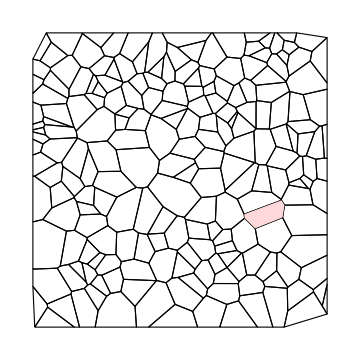

```mathematica
Show[plt,Graphics[{LightRed,Polygon@Lookup[indTopts,cellToVertexG[138]]}]]
```

```mathematica
{indToptsCG,cellToVertexCG,areaPolygonAssocCG,periPolygonAssocCG}=cellDivision[138,indTopts,areaPolygonAssoc,periPolygonAssoc,cellToVertexG];
```

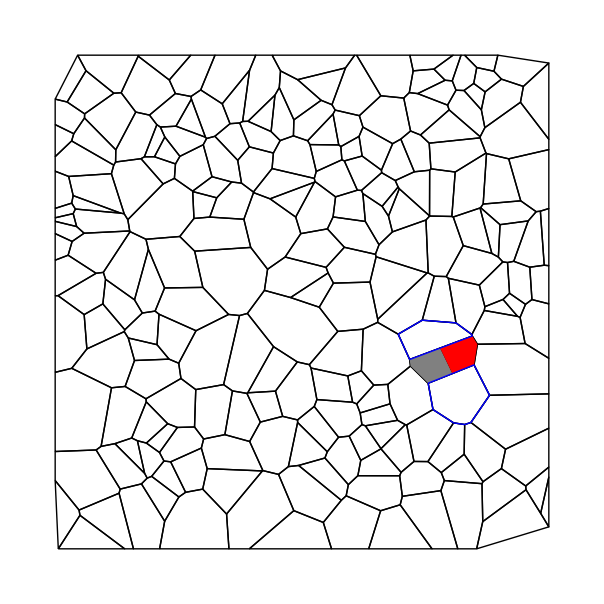

```mathematica
Graphics[{Black,Thick,Values@Map[Line[Join[##,{First@#}]]&@Lookup[indToptsCG,#]&,cellToVertexCG],
Gray,Polygon@Lookup[indToptsCG,cellToVertexCG[201]],Red,Polygon@Lookup[indToptsCG,cellToVertexCG[202]],
Blue,Line[Join[##,{First@#}]]&@Lookup[indToptsCG,cellToVertexCG[#]]&/@{94,154}}
]
```

```mathematica
TakeLargest[areaPolygonAssoc,5]
```

<|190→0.0160202,125→0.0158383,187→0.0146222,99→0.0138049,176→0.0132217|>

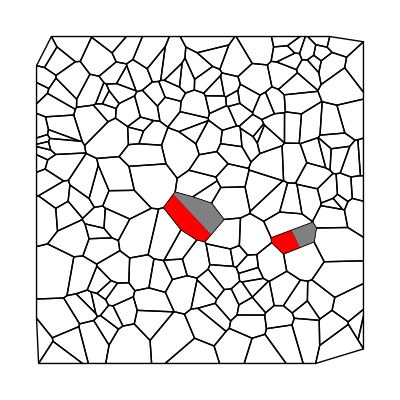

```mathematica
{indToptsCG,cellToVertexCG,areaPolygonAssocCG,periPolygonAssocCG}=cellDivision[190,indToptsCG,areaPolygonAssocCG,periPolygonAssocCG,cellToVertexCG];

Graphics[{Black,Thick,Values@Map[Line[Join[##,{First@#}]]&@Lookup[indToptsCG,#]&,cellToVertexCG],
Gray,Polygon@Lookup[indToptsCG,cellToVertexCG[204]],Red,Polygon@Lookup[indToptsCG,cellToVertexCG[203]],
Gray,Polygon@Lookup[indToptsCG,cellToVertexCG[202]],Red,Polygon@Lookup[indToptsCG,cellToVertexCG[201]]}]
```